```mathematica
pa={{0,0.5,0.5},{0.5,0,0.5},{0.5,0.5,0}}
uc={{1,0,0},{0,1,0},{0,0,1}}
```

{{0,0.5,0.5},{0.5,0,0.5},{0.5,0.5,0}}

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
pa.uc
```

{{0.,0.5,0.5},{0.5,0.,0.5},{0.5,0.5,0.}}

```mathematica
Inverse@pa
```

{{-1.,1.,1.},{1.,-1.,1.},{1.,1.,-1.}}

```mathematica
Inverse@uc
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
pa.{0.5,0.5,0.5}
pa.{0.5,0.5,0.25}
pa.{0.5,0.5,0}
pa.{0.25,0.25,0}
pa.{0.125,0.125,0}
pa.{0,0,0}
```

{0.5,0.5,0.5}

{0.375,0.375,0.5}

{0.25,0.25,0.5}

{0.125,0.125,0.25}

{0.0625,0.0625,0.125}

{0.,0.,0.}

```mathematica
(*Gamma to X*)
pa.{0,0,0}
pa.{0.125,0.125,0}
pa.{0.25,0.25,0}
pa.{0.375,0.375,0}
pa.{0.5,0.5,0}
```

{0.,0.,0.}

{0.0625,0.0625,0.125}

{0.125,0.125,0.25}

{0.1875,0.1875,0.375}

{0.25,0.25,0.5}

```mathematica
(*X to L*)
pa.{0.5,0.5,0}
pa.{0.5,0.5,0.125}
pa.{0.5,0.5,0.25}
pa.{0.5,0.5,0.375}
pa.{0.5,0.5,0.5}
```

{0.25,0.25,0.5}

{0.3125,0.3125,0.5}

{0.375,0.375,0.5}

{0.4375,0.4375,0.5}

{0.5,0.5,0.5}

```mathematica
(*L to G*)
pa.{0.5,0.5,0.5}
pa.{0.375,0.375,0.375}
pa.{0.25,0.25,0.25}
pa.{0.125,0.125,0.125}
pa.{0,0,0}
```

{0.5,0.5,0.5}

{0.375,0.375,0.375}

{0.25,0.25,0.25}

{0.125,0.125,0.125}

{0.,0.,0.}

```mathematica
ul={{1/0.21465294,0,0},{0,1/0.21465294,0},{0,0,1/0.21465294}}
url=Inverse[ul]
```

{{4.65868,0,0},{0,4.65868,0},{0,0,4.65868}}

{{0.214653,0.,0.},{0.,0.214653,0.},{0.,0.,0.214653}}

```mathematica
prl={{-0.21465294,0.21465294,0.21465294},{0.21465294,-0.21465294,0.21465294},{0.21465294,0.21465294,-0.21465294}}
pl=Inverse@prl
```

{{-0.214653,0.214653,0.214653},{0.214653,-0.214653,0.214653},{0.214653,0.214653,-0.214653}}

{{-1.14679×10^-15,2.32934,2.32934},{2.32934,1.50597×10^-16,2.32934},{2.32934,2.32934,1.29304×10^-16}}

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/Band_life_broadened/GammaToX"];
filesLINE={"lw.10","lw.300","lw.1000","lw.3800"};
(*Exclude the DOS with zero smearing*)
lineWidths=Table[ReadList[filesLINE[[i]],{Number,Number,Number,Number,Number,Number}],{i,1,filesLINE//Length}];
bands=ReadList["prim.bands",{Number,Number,Number,Number,Number,Number,Number}];
```

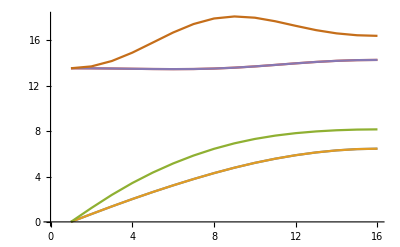

```mathematica
ListLinePlot@Transpose[bands][[2;;-1]]
```

```mathematica
Transpose[lineWidths[[1]]][[1]]//Length
```

16

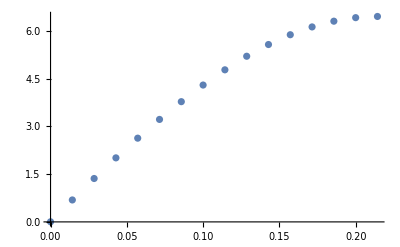

```mathematica
ListPlot@Transpose[{Transpose[bands][[1]],Transpose[bands][[2]]}]
```

```mathematica
Transpose[bands][[2]]//Length
```

16

InterpolatingFunction[{{0., 0.214286}}, <>]

InterpolatingFunction[{{0., 0.214286}}, <>]

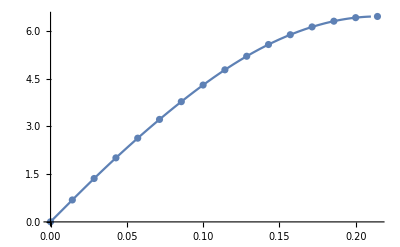

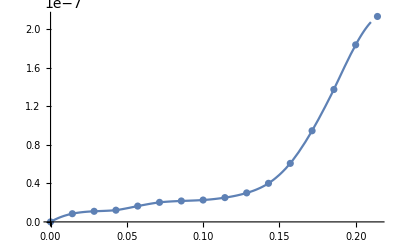

```mathematica
b1=Transpose[{Transpose[bands][[1]],Transpose[bands][[2]]}];
lw1=Transpose[{Transpose[bands][[1]],Transpose[lineWidths[[1]]][[1]]}];
interb1=Interpolation[b1]
interlw1=Interpolation[lw1]
Show[{ListPlot@b1,Plot[{interb1[x]},{x,0,0.21}]}]
Show[{ListPlot@lw1,Plot[{interlw1[x]},{x,0,0.21}]}]
```

```mathematica
Length[Transpose[bands]]
```

7

```mathematica
b=Table[Transpose[{Transpose[bands][[1]],Transpose[bands][[i+1]]}],{i,1,Length[Transpose[bands]]-1}];
lw10=Table[Transpose[{Transpose[bands][[1]],Transpose[lineWidths[[1]]][[i]]}],{i,1,Length[Transpose[lineWidths[[1]]]]}];
lw300=Table[Transpose[{Transpose[bands][[1]],Transpose[lineWidths[[2]]][[i]]}],{i,1,Length[Transpose[lineWidths[[2]]]]}];
lw1000=Table[Transpose[{Transpose[bands][[1]],Transpose[lineWidths[[3]]][[i]]}],{i,1,Length[Transpose[lineWidths[[3]]]]}];
lw3800=Table[Transpose[{Transpose[bands][[1]],Transpose[lineWidths[[4]]][[i]]}],{i,1,Length[Transpose[lineWidths[[4]]]]}];

interb=Table[Interpolation[b[[i]]],{i,1,Length[b]}];
interlw10=Table[Interpolation[lw10[[i]]],{i,1,Length[lw10]}];
interlw300=Table[Interpolation[lw300[[i]]],{i,1,Length[lw300]}];
interlw1000=Table[Interpolation[lw1000[[i]]],{i,1,Length[lw1000]}];
interlw3800=Table[Interpolation[lw3800[[i]]],{i,1,Length[lw3800]}];
```

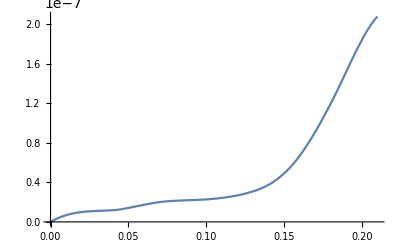

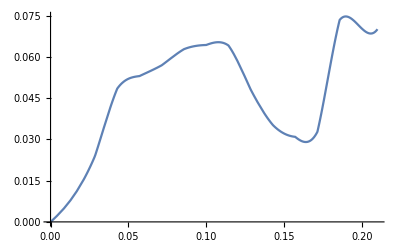

```mathematica
Plot[interlw10[[1]][x],{x,0,0.21}]
Plot[interlw3800[[1]][x],{x,0,0.21}]
```

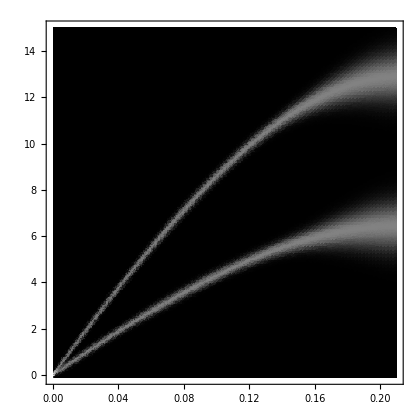

```mathematica
DensityPlot[Evaluate[4Log[1+interlw1[x]/interlw1[0.21]+0.05]*PDF[NormalDistribution[2interb1[x],Log[1+interlw1[x]/interlw1[0.21]+0.05]],y]+4Log[1+interlw1[x]/interlw1[0.21]+0.05]*PDF[NormalDistribution[interb1[x],Log[1+interlw1[x]/interlw1[0.21]+0.05]],y]],{x,0,0.21},{y,-0.1,15},PlotRange->All,PlotPoints->100,ColorFunction->GrayLevel]
```

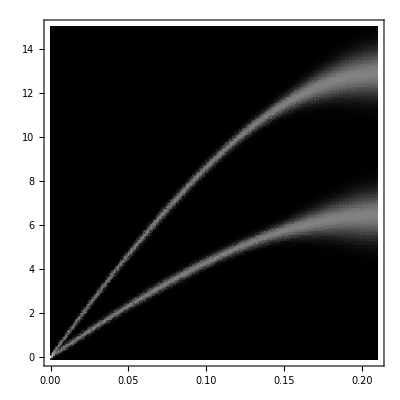

```mathematica
DensityPlot[Evaluate[4Log[1+interlw1[x]/interlw1[0.21]+0.05]*PDF[NormalDistribution[2interb1[x],Log[1+interlw1[x]/interlw1[0.21]+0.05]],y]+4Log[1+interlw1[x]/interlw1[0.21]+0.05]*PDF[NormalDistribution[interb1[x],Log[1+interlw1[x]/interlw1[0.21]+0.05]],y]],{x,0,0.21},{y,-0.1,15},PlotRange->All,PlotPoints->100,ColorFunction->GrayLevel]
```

-Graphics-

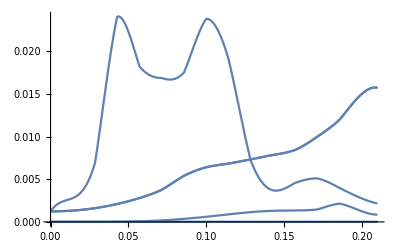

```mathematica
Plot[interlw10[[1]][x],{x,0,0.21}]
Plot[Table[interlw10[[i]][x],{i,1,6}],{x,0,0.21}]
```

```mathematica
FindMaxValue[interlw10[[6]][x],{x,0,0.21}]
```

0.0240878

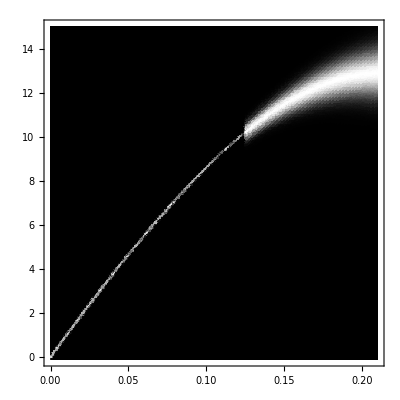

```mathematica
DensityPlot[Evaluate[4Log[1+interlw10[[1]][x]/interlw10[[1]][0.21]+0.05]*PDF[NormalDistribution[2interb[[1]][x],Log[1+interlw10[[1]][x]/interlw10[[1]][0.21]+0.05]],y]],{x,0,0.21},{y,-0.1,15},PlotRange->All,PlotPoints->100,ColorFunction->GrayLevel]
```

```mathematica
DensityPlot[Evaluate[],{x,0,0.21},{y,-0.1,15},PlotRange->All,PlotPoints->100,ColorFunction->GrayLevel]
```

```mathematica
broadBands10=Table[(2interlw10[[i]][x]/MaxValue[{interlw10[[i]][x],0<x<0.21},x])*PDF[NormalDistribution[interb[[i]][x],(0.05+1interlw10[[i]][x]/MaxValue[{interlw10[[i]][x],0<x<0.21},x])],y],{i,1,6}];
```

```mathematica
broadBands300=Table[(2interlw300[[i]][x]/MaxValue[{interlw300[[i]][x],0<x<0.21},x])*PDF[NormalDistribution[interb[[i]][x],(0.05+1interlw300[[i]][x]/MaxValue[{interlw300[[i]][x],0<x<0.21},x])],y],{i,1,6}];
```

```mathematica
broadBands1000=Table[(2interlw1000[[i]][x]/MaxValue[{interlw1000[[i]][x],0<x<0.21},x])*PDF[NormalDistribution[interb[[i]][x],(0.05+1interlw1000[[i]][x]/MaxValue[{interlw1000[[i]][x],0<x<0.21},x])],y],{i,1,6}];
```

```mathematica
broadBands3800=With[{height=2,width=2,baseWidth=0.02},Table[(height*interlw3800[[i]][x]/MaxValue[{interlw3800[[i]][x],0<x<0.21},x])*PDF[NormalDistribution[interb[[i]][x],(baseWidth+width*interlw3800[[i]][x]/MaxValue[{interlw3800[[i]][x],0<x<0.21},x])],y],{i,1,6}]];
Show[{DensityPlot[Total@broadBands,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->20,PlotPoints->100,FrameLabel->{Style["Reciprocal space",20],Style["Energy (eV)",20]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["10K",20]],Plot[Evaluate@Table[interb[[i]][x],{i,1,6}],{x,0,0.21},PlotStyle->Thickness[0.002],PlotLabel->"10K",PlotTheme->"Scientific",PlotLegends->SwatchLegend[{Style["TA_1",18],Style["TA_2",18],Style["LA",18],Style["TO_1",18],Style["TO_2",18],Style["LO",18]}]]}]
```

-Graphics-

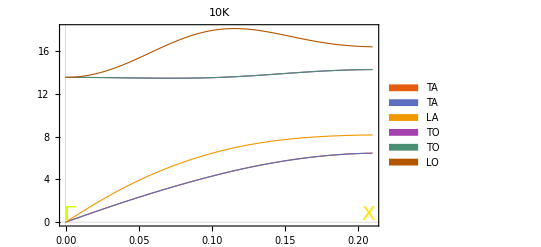

```mathematica
Show[{Plot[Evaluate@Table[interb[[i]][x],{i,1,6}],{x,0,0.21},PlotStyle->Thickness[0.002],PlotLabel->"10K",PlotTheme->"Scientific",PlotLegends->SwatchLegend[{Style["TA",18],Style["TA",18],Style["LA",18],Style["TO",18],Style["TO",18],Style["LO",18]}]],
Graphics[{Text[Style["Γ",20,FontFamily->"Times",Hue[0.2]],{0.003,0.7}]}],Graphics[{Text[Style["X",20,FontFamily->"Times",Hue[0.15]],{0.2073,0.7}]}]}]
```

```mathematica
1
```

```mathematica
broadBands10=With[{height=1.5,width=1.5,baseWidth=0.05},Table[(height*interlw10[[i]][x]/MaxValue[{interlw10[[i]][x],0<x<0.21},x])*PDF[NormalDistribution[interb[[i]][x],(baseWidth+width*interlw10[[i]][x]/MaxValue[{interlw10[[i]][x],0<x<0.21},x])],y],{i,1,6}]];
```

```mathematica
pBand10=Show[{DensityPlot[Total@broadBands10,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->20,PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20],Style["Energy (THz)",20]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["10K",20]],Plot[Evaluate@Table[interb[[i]][x],{i,1,6}],{x,0,0.21},PlotStyle->Thickness[0.002],PlotLabel->"10K",PlotTheme->"Scientific",PlotLegends->SwatchLegend[{Style["TA",18],Style["TA",18],Style["LA",18],Style["TO",18],Style["TO",18],Style["LO",18]}]],
Graphics[{Text[Style["Γ",25,Bold,FontFamily->"Times",Hue[0.13]],{0.006,1.2}]}],Graphics[{Text[Style["X",25,Bold,FontFamily->"Times",Hue[0.13]],{0.202,1.2}]}]}]
```

-Graphics-

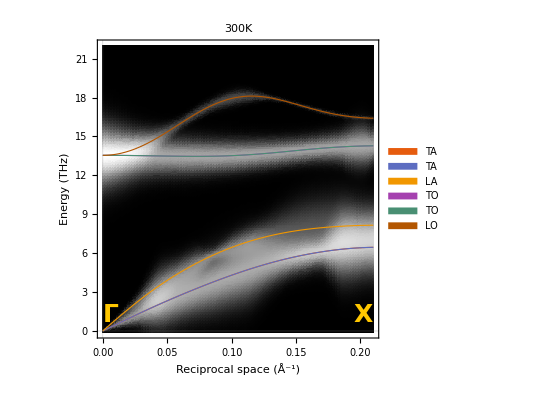

```mathematica
broadBands300=With[{height=1.5,width=1.5,baseWidth=0.05},Table[(height*interlw300[[i]][x]/MaxValue[{interlw300[[i]][x],0<x<0.21},x])*PDF[NormalDistribution[interb[[i]][x],(baseWidth+width*interlw300[[i]][x]/MaxValue[{interlw300[[i]][x],0<x<0.21},x])],y],{i,1,6}]];
pBand300=Show[{DensityPlot[Total@broadBands300,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->20,PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20],Style["Energy (THz)",20]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["300K",20]],Plot[Evaluate@Table[interb[[i]][x],{i,1,6}],{x,0,0.21},PlotStyle->Thickness[0.002],PlotLabel->"300K",PlotTheme->"Scientific",PlotLegends->SwatchLegend[{Style["TA",18],Style["TA",18],Style["LA",18],Style["TO",18],Style["TO",18],Style["LO",18]}]],
Graphics[{Text[Style["Γ",25,Bold,FontFamily->"Times",Hue[0.13]],{0.006,1.2}]}],Graphics[{Text[Style["X",25,Bold,FontFamily->"Times",Hue[0.13]],{0.202,1.2}]}]}]
```

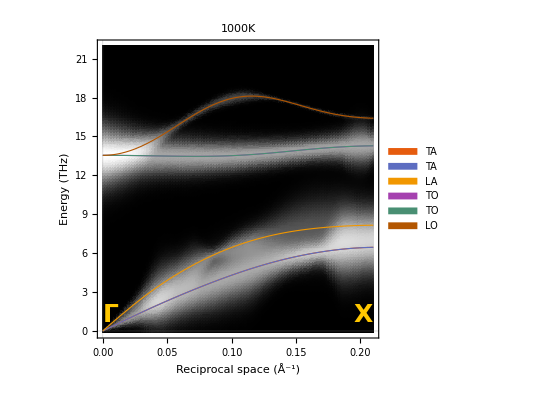

```mathematica
broadBands1000=With[{height=1.5,width=1.5,baseWidth=0.05},Table[(height*interlw1000[[i]][x]/MaxValue[{interlw1000[[i]][x],0<x<0.21},x])*PDF[NormalDistribution[interb[[i]][x],(baseWidth+width*interlw1000[[i]][x]/MaxValue[{interlw1000[[i]][x],0<x<0.21},x])],y],{i,1,6}]];
pBand1000=Show[{DensityPlot[Total@broadBands1000,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->20,PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20],Style["Energy (THz)",20]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["1000K",20]],Plot[Evaluate@Table[interb[[i]][x],{i,1,6}],{x,0,0.21},PlotStyle->Thickness[0.002],PlotLabel->"1000K",PlotTheme->"Scientific",PlotLegends->SwatchLegend[{Style["TA",18],Style["TA",18],Style["LA",18],Style["TO",18],Style["TO",18],Style["LO",18]}]],
Graphics[{Text[Style["Γ",25,Bold,FontFamily->"Times",Hue[0.13]],{0.006,1.2}]}],Graphics[{Text[Style["X",25,Bold,FontFamily->"Times",Hue[0.13]],{0.202,1.2}]}]}]
```

```mathematica
broadBands3800=With[{height=1.5,width=1.5,baseWidth=0.05},Table[(height*interlw3800[[i]][x]/MaxValue[{interlw3800[[i]][x],0<x<0.21},x])*PDF[NormalDistribution[interb[[i]][x],(baseWidth+width*interlw3800[[i]][x]/MaxValue[{interlw3800[[i]][x],0<x<0.21},x])],y],{i,1,6}]];
Show[{DensityPlot[Total@broadBands3800,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->20,PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20],Style["Energy (THz)",20]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["3800K",20]],Plot[Evaluate@Table[interb[[i]][x],{i,1,6}],{x,0,0.21},PlotStyle->Thickness[0.002],PlotLabel->"3800K",PlotTheme->"Scientific",PlotLegends->SwatchLegend[{Style["TA",18],Style["TA",18],Style["LA",18],Style["TO",18],Style["TO",18],Style["LO",18]}]],
Graphics[{Text[Style["Γ",25,Bold,FontFamily->"Times",Hue[0.13]],{0.006,1.2}]}],Graphics[{Text[Style["X",25,Bold,FontFamily->"Times",Hue[0.13]],{0.202,1.2}]}]}]
```

-Graphics-

```mathematica
Plot[Evaluate@Table[interb[[i]][x],{i,1,6}],{x,0,0.21},PlotStyle->Thickness[0.01]]
```

-Graphics-

```mathematica
Plot[Evaluate@{interb[[1]][x],interb[[3]][x],interb[[4]][x],interb[[6]][x]},{x,0,0.21},PlotStyle->Thickness[0.01],PlotLegends->SwatchLegend[{"LA","TA","LO","TO"}]]
```

-Graphics-

```mathematica
Plot[Evaluate@{interlw10[[1]][x],interlw10[[3]][x],interlw10[[4]][x],interlw10[[6]][x]},{x,0,0.21},PlotLegends->SwatchLegend[{"LA","TA_1","LO","TO_1"}]]
Plot[Evaluate@{interlw300[[1]][x],interlw300[[3]][x],interlw300[[4]][x],interlw300[[6]][x]},{x,0,0.21},PlotLegends->SwatchLegend[{"LA","TA_1","LO","TO_1"}]]
Plot[Evaluate@{interlw1000[[1]][x],interlw1000[[3]][x],interlw1000[[4]][x],interlw1000[[6]][x]},{x,0,0.21},PlotLegends->SwatchLegend[{"LA","TA_1","LO","TO_1"}]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Plot[Evaluate[Table[interlw10[[i]][x]/MaxValue[{interlw10[[i]][x],0<x<0.21},x],{i,1,6}]],{x,0,0.21},PlotLegends->SwatchLegend[{"LA","TA_1","TA_2""LO","TO_1","TO_2"}]]
```

-Graphics-

```mathematica
p10=DensityPlot[Total@broadBands,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicks->False,FrameTicksStyle->20,PlotPoints->100,ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["10K",20]];
p300=DensityPlot[Total@broadBands300,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicks->False,FrameTicksStyle->20,PlotPoints->100,ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["300K",20]];
p1000=DensityPlot[Total@broadBands1000,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicks->False,FrameTicksStyle->20,PlotPoints->100,ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["1000K",20]];
p3800=DensityPlot[Total@broadBands3800,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicks->False,FrameTicksStyle->20,PlotPoints->100,ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["3800K",20]];
```

```mathematica
GraphicsGrid[{{p10,p300},{p1000,p3800}},ImageSize->800]
```

-Graphics-

```mathematica
LogPlot[Evaluate[Table[interlw10[[i]][x],{i,1,6}]],{x,0,0.21},PlotLegends->SwatchLegend[{"LA","TA_1","TA_2""LO","T0_1","T0_2"}]]
```

-Graphics-

```mathematica
Plot[Evaluate[Table[interlw10[[i]][x],{i,1,6}]],{x,0,0.21},PlotLegends->SwatchLegend[{"LA","TA_1","TA_2""LO","T0_1","T0_2"}]]
```

-Graphics-

```mathematica
Plot[Evaluate[Log@Table[interlw10[[i]][x]+1,{i,1,6}]],{x,0,0.21}]
Plot[Evaluate[Table[interlw10[[i]][x],{i,1,6}]],{x,0,0.21}]
Plot[Evaluate[Table[interlw10[[i]][x]+1,{i,1,6}]],{x,0,0.21}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
With[{height=1,width=0.66,baseWidth=0.01},Table[(height*(interlw10[[i]][x]+1))*PDF[NormalDistribution[interb[[i]][x],(baseWidth+width*(interlw10[[i]][x]+1))],y],{i,1,6}]];
broad10=Show[{DensityPlot[Total@%,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->20,PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20],Style["Energy (THz)",20]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["10K",20]],Plot[Evaluate@Table[interb[[i]][x],{i,1,6}],{x,0,0.21},PlotStyle->Thickness[0.002],PlotLabel->"10K",PlotTheme->"Scientific",PlotLegends->SwatchLegend[{Style["TA",18],Style["TA",18],Style["LA",18],Style["TO",18],Style["TO",18],Style["LO",18]}]],
Graphics[{Text[Style["Γ",25,Bold,FontFamily->"Times",Hue[0.13]],{0.006,1.2}]}],Graphics[{Text[Style["X",25,Bold,FontFamily->"Times",Hue[0.13]],{0.202,1.2}]}]}]
```

-Graphics-

```mathematica
Plot[Evaluate@{interb[[1]][x],interb[[3]][x],interb[[4]][x],interb[[6]][x]},{x,0,0.21},PlotStyle->Thickness[0.01],PlotTheme->"Scientific",PlotLegends->SwatchLegend[{Style["TA",18],Style["LA",18],Style["TO",18],Style["LO",18]}]]
```

-Graphics-

```mathematica
With[{height=1.5,width=1.5,baseWidth=0.1},Table[(baseWidth+height*(interlw10[[i]][x]))*PDF[NormalDistribution[interb[[i]][x],(baseWidth+width*(interlw10[[i]][x]))],y],{i,1,6}]];
Show[{DensityPlot[Total@%,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->20,PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20],Style["Energy (THz)",20]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["10K",20]],Plot[Evaluate@{interb[[1]][x],interb[[3]][x],interb[[4]][x],interb[[6]][x]},{x,0,0.21},PlotStyle->Thickness[0.005],PlotTheme->"Scientific",PlotLegends->SwatchLegend[{Style["TA",18],Style["LA",18],Style["TO",18],Style["LO",18]}]],
Graphics[{Text[Style["Γ",25,Bold,FontFamily->"Times",Hue[0.13]],{0.006,1.2}]}],Graphics[{Text[Style["X",25,Bold,FontFamily->"Times",Hue[0.13]],{0.202,1.2}]}]}]
```

-Graphics-

```mathematica
With[{height=1.5,width=1.5,baseWidth=0.1},Table[(baseWidth+height*(interlw1000[[i]][x]))*PDF[NormalDistribution[interb[[i]][x],(baseWidth+width*(interlw1000[[i]][x]))],y],{i,1,6}]];
Show[{DensityPlot[Total@%,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->20,PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20],Style["Energy (THz)",20]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["1000K",20]],Plot[Evaluate@{interb[[1]][x],interb[[3]][x],interb[[4]][x],interb[[6]][x]},{x,0,0.21},PlotStyle->Thickness[0.005],PlotTheme->"Scientific",PlotLegends->SwatchLegend[{Style["TA",18],Style["LA",18],Style["TO",18],Style["LO",18]}]],
Graphics[{Text[Style["Γ",25,Bold,FontFamily->"Times",Hue[0.13]],{0.006,1.2}]}],Graphics[{Text[Style["X",25,Bold,FontFamily->"Times",Hue[0.13]],{0.202,1.2}]}]}]
```

-Graphics-

```mathematica
With[{height=1.5,width=1.5,baseWidth=0.1},Table[(baseWidth+height*(interlw3800[[i]][x]))*PDF[NormalDistribution[interb[[i]][x],(baseWidth+width*(interlw3800[[i]][x]))],y],{i,1,6}]];
Show[{DensityPlot[Total@%,{x,0,0.21},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->20,PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20],Style["Energy (THz)",20]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["3800K",20]],Plot[Evaluate@{interb[[1]][x],interb[[3]][x],interb[[4]][x],interb[[6]][x]},{x,0,0.21},PlotStyle->Thickness[0.005],PlotTheme->"Scientific",PlotLegends->SwatchLegend[{Style["TA",18],Style["LA",18],Style["TO",18],Style["LO",18]}]],
Graphics[{Text[Style["Γ",25,Bold,FontFamily->"Times",Hue[0.13]],{0.006,1.2}]}],Graphics[{Text[Style["X",25,Bold,FontFamily->"Times",Hue[0.13]],{0.202,1.2}]}]}]
```

-Graphics-